Correlation

FFCS paclet:Fretica/tutorial/Correlation#33963545 | Correlation of arbitrary time eventspaclet:Fretica/tutorial/Correlation#135960150
FFCSW  paclet:Fretica/tutorial/Correlation#362226427 | Correlation of binned datapaclet:Fretica/tutorial/Correlation#111714022
FnsFCSpaclet:Fretica/tutorial/Correlation#772237054 | Example for how to combine a series of ns-FCS measurements (HappyBunch) paclet:Fretica/tutorial/Correlation#17169443

```mathematica
Needs["Fretica`"]
```

FFCS

### Overview FFCS

```mathematica
?FFCS
```

### Load some data

```mathematica
(*typical settings for a two channel FRET measurement*)
FEnablePie[False];
FSetFRETRoutes[{"A","D"}](* detector1: acceptor, detector2: donor*)
FSetRCM[{{1,-0.06},{-0.008,1.25}}];(*γ=1.25, Subscript[β, D->A]=0.06, Subscript[β, A->D]=0.008*)
FSetDirectAcceptorExcitation[0.05];
FOpenTTTR[$FreticaExamples<>"\\1.00GdmClA.t3r"] (*Csp near the folding midpoint*)
FDetermineBackground[](*returns estimated background rates in counts per seconds*)
```

1

{2751.13,3067.25,0.,0.,0.,0.}

### Single correlations: FFCS[lagtimes, route1, route2] FFCS[lagtimes, route1, route2, tstart, tstop]

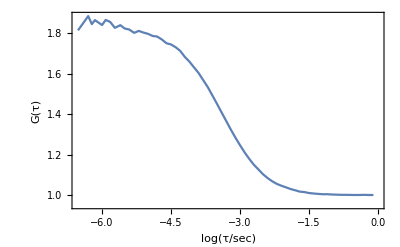

```mathematica
FFCS[-6.5,0.,0.1,{1,0,0,0},{0,1,0,0},FOutput->FGraph]
```

```mathematica
FFCS[-6.5,0.,0.1,{1,0,0,0},{0,1,0,0},FOutput->FData]
```

{{3.×10^-7,1.81446},{5.×10^-7,1.8849},{6.×10^-7,1.8454},{7.×10^-7,1.86515},{1.×10^-6,1.84096},{1.2×10^-6,1.86592},{1.5×10^-6,1.85635},{1.9×10^-6,1.82708},{2.5×10^-6,1.84014},{3.1×10^-6,1.82388},{3.9×10^-6,1.81856},{5.×10^-6,1.80233},{6.3×10^-6,1.81191},{7.9×10^-6,1.8038},{0.00001,1.79732},{0.0000125,1.78706},{0.0000158,1.78384},{0.0000199,1.76965},{0.0000251,1.75097},{0.0000316,1.74481},{0.0000398,1.73119},{0.0000501,1.71306},{0.000063,1.68338},{0.0000794,1.65991},{0.0001,1.63133},{0.0001258,1.6034},{0.0001584,1.56835},{0.0001995,1.53345},{0.0002511,1.49247},{0.0003162,1.45096},{0.0003981,1.40826},{0.0005011,1.36634},{0.0006309,1.32385},{0.0007943,1.28416},{0.001,1.2466},{0.0012589,1.21116},{0.0015848,1.17926},{0.0019952,1.15011},{0.0025118,1.12676},{0.0031622,1.10288},{0.003981,1.08415},{0.0050118,1.0682},{0.0063095,1.05535},{0.0079432,1.04628},{0.01,1.03818},{0.0125892,1.02992},{0.0158489,1.02378},{0.0199526,1.01711},{0.0251188,1.01495},{0.0316227,1.01015},{0.0398107,1.00784},{0.0501187,1.00585},{0.0630957,1.00422},{0.0794328,1.00438},{0.1,1.00285},{0.125893,1.00216},{0.158489,1.00125},{0.199526,1.00126},{0.251189,1.00082},{0.316228,1.0005},{0.398107,1.00058},{0.501187,1.00117},{0.630957,1.00045},{0.794328,1.00047}}

```mathematica
FFCS[-6.5, 0., 0.1, {1, 0, 0, 0}, {0, 1, 0, 0}, FOutput -> FRawData]
```

{CorrelikonTmeasure→35999993444,CorrelikonTimeUnitSec→1.×10^-7,CorrelikonTauBins→{3,5,6,7,10,12,15,19,25,31,39,50,63,79,100,125,158,199,251,316,398,501,630,794,1000,1258,1584,1995,2511,3162,3981,5011,6309,7943,10000,12589,15848,19952,25118,31622,39810,50118,63095,79432,100000,125892,158489,199526,251188,316227,398107,501187,630957,794328,1000000,1258925,1584893,1995262,2511886,3162277,3981071,5011872,6309573,7943282,10000000},CorrelikonN12→{{11024,9904063,11042084},{5726,9904063,11042084},{5606,9904063,11042084},{16998,9904063,11042084},{11185,9904063,11042084},{17005,9904063,11042084},{22557,9904063,11042084},{33302,9904063,11042084},{33540,9904063,11042084},{44325,9904063,11042084},{60769,9904063,11042084},{71177,9904063,11042084},{88068,9904063,11042084},{115072,9904063,11042084},{136498,9904063,11042084},{179149,9904063,11042084},{222178,9904063,11042084},{279545,9904063,11042084},{345744,9904063,11042084},{434634,9904063,11042084},{541682,9904063,11042084},{671311,9904063,11042084},{838664,9904063,11042084},{1038755,9904063,11042084},{1278564,9904063,11042084},{1587889,9904063,11042084},{1958159,9904063,11042084},{2403709,9904063,11042084},{2951538,9904063,11042084},{3609942,9904063,11042084},{4406391,9904063,11042084},{5387612,9904063,11042084},{6571333,9904063,11042084},{8024425,9904063,11042084},{9804440,9904063,11042084},{11990747,9904063,11042084},{14702130,9904063,11042084},{18049043,9904063,11042084},{22262483,9904063,11042084},{27432664,9904063,11042084},{33948875,9904063,11042084},{42110181,9904063,11042084},{52375555,9904063,11042084},{65373401,9904063,11042084},{81658020,9904063,11042084},{101986021,9904063,11042084},{127626820,9904063,11042084},{159623828,9904063,11042084},{200529402,9904063,11042084},{251258286,9904063,11042084},{315588482,9904063,11042084},{396518608,9904063,11042084},{498375039,9904063,11042084},{627517492,9904063,11042084},{788785909,9904063,11042084},{992328229,9904063,11042084},{1248118509,9904063,11042084},{1571296088,9904063,11042084},{1977238116,9904063,11042084},{2488340182,9904063,11042084},{3132799850,9904063,11042084},{3946176725,9904063,11042084},{4964147650,9904063,11042084},{6249338846,9904063,11042084}},CorrelikonG12→{1.81446,1.8849,1.8454,1.86515,1.84096,1.86592,1.85635,1.82708,1.84014,1.82388,1.81856,1.80233,1.81191,1.8038,1.79732,1.78706,1.78384,1.76965,1.75097,1.74481,1.73119,1.71306,1.68338,1.65991,1.63133,1.6034,1.56835,1.53345,1.49247,1.45096,1.40826,1.36634,1.32385,1.28416,1.2466,1.21116,1.17926,1.15011,1.12676,1.10288,1.08415,1.0682,1.05535,1.04628,1.03818,1.02992,1.02378,1.01711,1.01495,1.01015,1.00784,1.00585,1.00422,1.00438,1.00285,1.00216,1.00125,1.00126,1.00082,1.0005,1.00058,1.00117,1.00045,1.00047}}

The same as above but only of the first 100 seconds (last two parameters are tstart and tstop in seconds

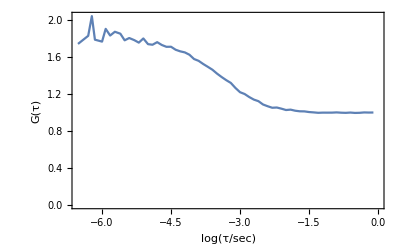

```mathematica
correldat=FFCS[-6.5,0.,0.1,{1,0,0,0},{0,1,0,0},0,100,FOutput->FGraph]
```

Arbitrary lag times can be given in a list:

```mathematica
tau=Table[10^logt,{logt,-6.5,0.,0.1}];
correldat=FFCS[tau,{1,0,0,0},{0,1,0,0},FOutput->FGraph]
```

-Graphics-

### Single correlations with lifetime channel constraints FFCS[lagtimes, route1, route2, {c11, c12}, {c21, c22}] FFCS[lagtimes, route1, route2, {c11, c12}, {c21, c22}, tstart, tstop]

Load some PIE data

```mathematica
FOpenTTTR[$FreticaExamples<>"\\RhoK_5M_30min_a.t3r"];
```

```mathematica
ListPlot[FLifeTimeHisto[FRoutes->{1,2},FPhotonData->All,FOutput->FData][[All,1;;4096,2]],PlotRange->All]
```

-Graphics-

Correlate channel {2800,3000}:

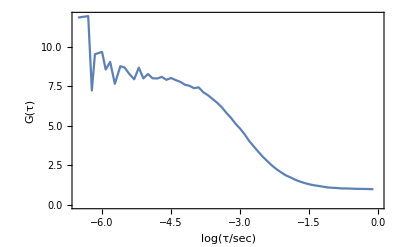

```mathematica
correldat=FFCS[-6.5,0.,0.1,{1,0,0,0},{1,0,0,0},{2800,3000},{2800,3000},FOutput->FGraph]
```

### Multiple correlations between different detection route pairs {ri1, ri2}, i=1,2,3,... FFCS[lagtimes, {{r11, r12}, {r21, r22}, ...}] FFCS[lagtimes, {{r11, r12}, {r21, r22}, ...}, tstart, tstop] FFCS[lagtimes, {{r11, r12}, {r21, r22}, ...}, {c11, c12}, {c21, c22}] FFCS[lagtimes, {{r11, r12}, {r21, r22}, ...}, {c11, c12}, {c21, c22}, tstart, tstop]

Whenever one wants to calculate more then one FCS from the loaded TTTR file one can used parallelized calculations. If enough CPU kernels are available  the total calculation time is about the same time as for a single FCS calculation.

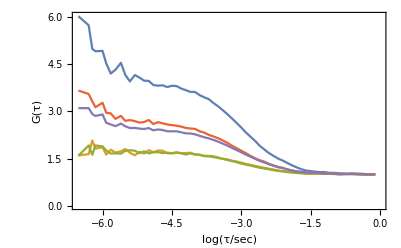

```mathematica
correldat=FFCS[-6.5,0.,0.1,
{
{{1,0,0,0},{1,0,0,0}},
{{1,0,0,0},{0,1,0,0}},
{{0,1,0,0},{1,0,0,0}},
{{0,1,0,0},{0,1,0,0}},
{{1,1,0,0},{1,1,0,0}}
}
,0,100,FOutput->FGraph]
```

### Multiple correlations between different detection route and channel constraints pairs {{ri1, {ci1a, ci1b}}, {ri2, {ci2a, ci2b}}}, i=1,2,3,... FFCS[lagtimes, {{r11, r12}, {r21, r22}, ...}] FFCS[lagtimes, {{r11, r12}, {r21, r22}, ...}, tstart, tstop] FFCS[lagtimes, {{r11, r12}, {r21, r22}, ...}, {c11, c12}, {c21, c22}] FFCS[lagtimes, {{r11, r12}, {r21, r22}, ...}, {c11, c12}, {c21, c22}, tstart, tstop]

This is the most general form of FFCS

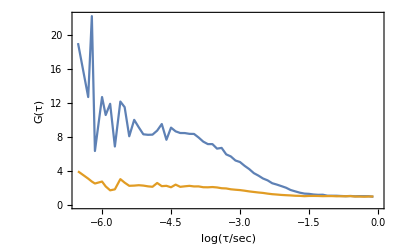

```mathematica
correldat=FFCS[-6.5,0.,0.1,
{
{{{1,0,0,0},{2800,3000}},{{1,0,0,0},{2800,3000}}},
{{{1,1,0,0},{1900,2500}},{{1,1,0,0},{2800,3000}}}
}
,0,100,FOutput->FGraph]
```

FFCSW

#### Overview FFCSW

```mathematica
?FFCSW
```

FnsFCS

### FnsFCS[ route1, route2,{τ1,τ2,Δτ }] FnsFCS[ route1, route2,{τ1,τ2,Δτ }, tstart, tstop] FnsFCS[ {{r11, r12}, {r21, r22}, ...},{τ1,τ2,Δτ }, tstart, tstop]

```mathematica
?FnsFCS
```

```mathematica
FOpenTTTR[$FreticaExamples<>"\\1.00GdmClA.t3r"]; (*Csp near the folding midpoint*)
```

```mathematica
AbsoluteTiming[correldat=FnsFCS[{1,0,0,0},{0,1,0,0},{-100,100,0.1}];]
ListPlot[Drop[correldat,1],Joined->True,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"τ (μs)", "G(τ)"},LabelStyle->{FontFamily-> "Helvetica",FontSize-> Medium,FontWeight-> Bold}]
```

{0.356589,Null}

-Graphics-

Only the first 100 seconds.

```mathematica
AbsoluteTiming[correldat=FnsFCS[{1,0,0,0},{0,1,0,0},{-100,100,0.1},0,100];]
ListPlot[Drop[correldat,1],Joined->True,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"τ (μs)", "G(τ)"},LabelStyle->{FontFamily-> "Helvetica",FontSize-> Medium,FontWeight-> Bold}]
```

{0.0107882,Null}

-Graphics-

Note: The apparent "antibunching" peak is only due to the time resolution of the TimeHarp (100 ns).

Correlation of arbitrary time events

```mathematica
?FTimeCorrelate
```

```mathematica
FOpenTTTR[$FreticaExamples<>"\\1.00GdmClA.t3r"] (*Csp near the folding midpoint*)
FDetermineBackground[](*returns estimated background rates in counts per seconds*)
FFindBurstsDeltaT[0.00015,50,10000]
FDetermineBackground[]
```

1

{2751.13,3067.25,0.,0.,0.,0.}

18372

{2510.34,2919.52,0.,0.,0.,0.}

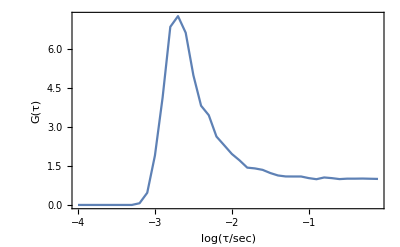

```mathematica
tau=Table[10^logt,{logt,-4.,0.,0.1}];
bursttimes=FGetFromBurstList[Mean[{"EndTime","StartTime"}]];
correldat=FTimeCorrelate[tau,bursttimes,bursttimes];

logcorreldat=Map[{Log[10,#[[1]]],#[[2]]}&,correldat];
ListPlot[logcorreldat,Joined->True,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"log(τ/sec)", "G(τ)"},LabelStyle->{FontFamily-> "Helvetica",FontSize-> Medium,FontWeight-> Bold}]
```

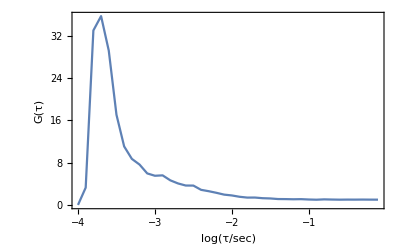

```mathematica
tau=Table[10^logt,{logt,-4.,0.,0.1}];
bt1=FGetFromBurstList["EndTime"];
bt2=FGetFromBurstList["StartTime"];
correldat=FTimeCorrelate[tau,bt1,bt2];

logcorreldat=Map[{Log[10,#[[1]]],#[[2]]}&,correldat];
ListPlot[logcorreldat,Joined->True,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"log(τ/sec)", "G(τ)"},LabelStyle->{FontFamily-> "Helvetica",FontSize-> Medium,FontWeight-> Bold}]
```

Correlation of binned data

```mathematica
?FCorrelateBinnedData
```

```mathematica
FFindBurstsFromTimeBinnedData[1,20,100,10000,FCombineContiguousBins->False]
elist=FGetFromBurstList["E"];
```

66282

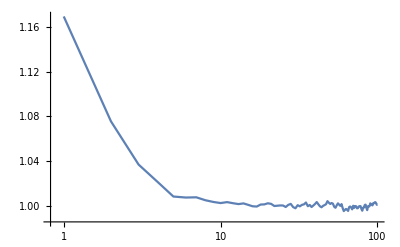

```mathematica
ListLogLinearPlot[FCorrelateBinnedData[elist,elist,100],PlotRange->All,Joined->True]
```

Example for how to combine a series of ns-FCS measurements (HappyBunch)

HappyBunch calculates for individual measurement files the correlation functions and saves the results under the symbol happybunch.

```mathematica
HappyBunch[fn_?FileExistsQ]:=Module[{st,k,Δ,logcorreldat,fcspl,tau,correldat,bunchpl,mcspl},
(*some functions to plot intermediate results*)
bunchpl:=Map[ListPlot[Drop[#,1],Joined->True,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"τ (μs)", "G(τ)"},LabelStyle->{FontFamily-> "Helvetica",FontSize-> Medium,FontWeight-> Bold}]&,correldat];
logcorreldat:=Map[{Log[10,#[[1]]],#[[2]]}&,correldat,{2}];
fcspl:=Map[ListPlot[#,Joined->True,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"log(τ/sec)", "G(τ)"},LabelStyle->{FontFamily-> "Helvetica",FontSize-> Medium,FontWeight-> Bold}]&,logcorreldat];
mcspl:=ListPlot[correldat,PlotStyle->{Red,Green},Joined->True,PlotRange->All,ImageSize->600,AspectRatio->0.2,Axes->False,Frame->True,FrameLabel->{"time (sec)","photons"},LabelStyle->{FontFamily-> "Helvetica",FontSize-> Medium,FontWeight-> Bold},FrameStyle-> Directive[Black,AbsoluteThickness[1]]];

(*define lag times for FCS*)
st=0;
tau={};k=0;Δ=10.^-9;If[Δ≤0,Δ=1.];
While[st<1.,AppendTo[tau,Table[st+= Δ 2^k,{n,0,6}]];k++;];
tau=Flatten[tau];
tau=Select[tau,#≤1.&];

(*Here the correlations are calculated and stored in happybunch[fn,..]*)
Print[fn];
FOpenTTTR[fn];
correldat={happybunch[fn,"bAA"],happybunch[fn,"bDD"],happybunch[fn,"bAD"]}=FnsFCS[{{{1,0,0,0},{0,0,1,0}},{{0,1,0,0},{0,0,0,1}},{{1,0,1,0},{0,1,0,1}}},{-5,5,0.001}];
Print@bunchpl;
correldat={happybunch[fn,"gAA"],happybunch[fn,"gDD"],happybunch[fn,"gAD"]}=FFCS[tau,{{{1,0,0,0},{0,0,1,0}},{{0,1,0,0},{0,0,0,1}},{{1,0,1,0},{0,1,0,1}}}];
Print@fcspl;
happybunch[fn,"mcs"]=correldat=FMCStrace[{{1,0,1,0},{0,1,0,1}},1000.,0,36000.,FOutput->FData];
Print@mcspl;
(*The results are saved and can be loaded again with Get[fn<>"_FCS.mat"]*)
Save[fn<>"_FCS.mat",happybunch];
]
```

Map HappyBunch over a list of files belonging to a series.

```mathematica
Map[HappyBunch,filelist]
```

Read the saved files

```mathematica
(*Read all calculated FCS data*)
Map[Get[#<>"_FCS.mat"]&,filelist]
```

Calculate the mean correlation curves

```mathematica
bDD=Mean[Map[happybunch[#,"bDD"]&,filelist]];
bAD=Mean[Map[happybunch[#,"bAD"]&,filelist]];
bAA=Mean[Map[happybunch[#,"bAA"]&,filelist]];

gDD=Mean[Map[happybunch[#,"gDD"]&,filelist]];
gAD=Mean[Map[happybunch[#,"gAD"]&,filelist]];
gAA=Mean[Map[happybunch[#,"gAA"]&,filelist]];
```

| Related Guides
▪Fretica